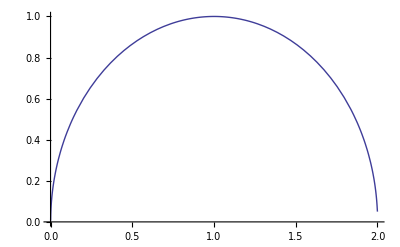

```mathematica
Plot[√(0.0012499999999999178 -(x-2)^2+0.5249921862789153 Sqrt[5.669102988825614*^-6+14.494762521716623 (x-2)^2]),{x,0,2}]
```

```mathematica
Polar={0.1,0.02};
```

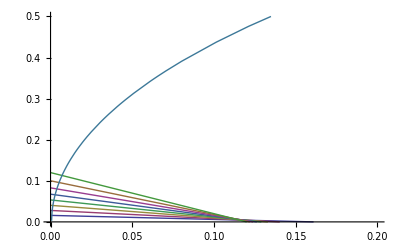

```mathematica
XX1=Table[(i-1)*0.002,{i,1,11}];
Ang1=Table[(i)*(45/8),{i,1,8}];
Y1=-Tan[Ang1*Pi/180]*(x-0.1)+XX1[[4;;11]];
Plot[{Y1,√(0.0012499999999999178 -(x-2)^2+0.5249921862789153 Sqrt[5.669102988825614*^-6+14.494762521716623 (x-2)^2])},{x,0,1},PlotRange->{{0,0.2},{0,0.5}}]
```

```mathematica
Y1
```

{-(-0.1+x) Tan[π/32],0.002-(-0.1+x) Tan[π/16],0.004-(-0.1+x) Tan[(3 π)/32],0.006-(-0.1+x) Tan[π/8],0.008-(-0.1+x) Tan[(5 π)/32],0.01-(-0.1+x) Tan[(3 π)/16],0.012-(-0.1+x) Tan[(7 π)/32],0.114-x}

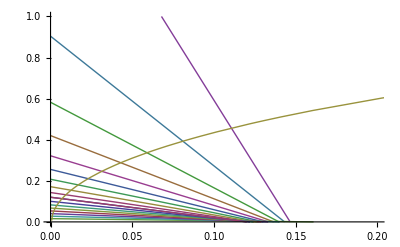

```mathematica
XX2=Table[Polar[[1]]+(i-1)*(0.05/10),{i,1,11}];
Ang2=Table[45+(i-1)*(45/10),{i,1,11}];
Y2=-Tan[Ang2*Pi/180]*(x-XX2)+Polar[[2]];
Plot[{Y2,Y1,√(0.0012499999999999178 -(x-2)^2+0.5249921862789153 Sqrt[5.669102988825614*^-6+14.494762521716623 (x-2)^2])},{x,0,2},PlotRange->{{0,0.2},{0,1}}]
```

```mathematica
Y1
```

{0.006-(-0.1+x) Tan[π/32],0.008-(-0.1+x) Tan[π/16],0.01-(-0.1+x) Tan[(3 π)/32],0.012-(-0.1+x) Tan[π/8],0.014-(-0.1+x) Tan[(5 π)/32],0.016-(-0.1+x) Tan[(3 π)/16],0.018-(-0.1+x) Tan[(7 π)/32],0.12-x}

```mathematica
Y2
```

{0.12-x,0.02-(-0.105+x) Cot[(9 π)/40],0.02-√(1+2/(√5)) (-0.11+x),0.02-(-0.115+x) Cot[(7 π)/40],0.02-(-0.12+x) Cot[(3 π)/20],0.02-(-0.125+x) Cot[π/8],0.02-√(5+2 √5) (-0.13+x),0.02-(-0.135+x) Cot[(3 π)/40],0.02-(-0.14+x) Cot[π/20],0.02-(-0.145+x) Cot[π/40],ComplexInfinity}

```mathematica
PT1=Flatten[Table[NSolve[√(0.0012499999999999178 -(x-2)^2+0.5249921862789153 Sqrt[5.669102988825614*^-6+14.494762521716623 (x-2)^2])==Y1[[i]],x],{i,1,Dimensions[Y1][[1]]}],1]
PT2=Flatten[Table[NSolve[{√(0.0012499999999999178 -(x-2)^2+0.5249921862789153 Sqrt[5.669102988825614*^-6+14.494762521716623 (x-2)^2])==Y2[[i]]},x],{i,1,Dimensions[Y2][[1]]-1}],1]
```

{{x→0.000749536},{x→0.00100856},{x→0.00142156},{x→0.00200887},{x→0.00280238},{x→0.00384996},{x→0.00522273},{x→0.00702703}}

{{x→0.00702703},{x→0.00937101},{x→0.01257},{x→0.016957},{x→0.0230028},{x→0.0313676},{x→0.0429595},{x→0.0589856},{x→0.080967},{x→0.110681}}

```mathematica
FindRoot[√(0.0012499999999999178 -(x-2)^2+0.5249921862789153 Sqrt[5.669102988825614*^-6+14.494762521716623 (x-2)^2])==0.002,{x,0.1}]
```

{x→0.000627098}

```mathematica
PT3=Flatten[Table[FindRoot[√(0.0012499999999999178 -(x-2)^2+0.5249921862789153 Sqrt[5.669102988825614*^-6+14.494762521716623 (x-2)^2])==XX1[[i]],{x,0.1}],{i,2,3}],1]
```

{x→0.000627098,x→0.000633098}

```mathematica
XX1[[2]]
```

0.002

```mathematica
h1=Table[Sqrt[(Y1[[i]]-XX1[[i]])^2+(x-Polar[[1]])^2]/.PT1[[i]],{i,1,7}]
h2=Table[Sqrt[(Polar[[2]]-Y2[[i]])^2+(x-XX2[[i]])^2]/.PT2[[i]],{i,1,Dimensions[PT2][[1]]}]
h3=Flatten[{(Polar[[1]]-x)/.PT3[[1]],(Polar[[1]]-x)/.PT3[[2]]}]
h4={Polar[[1]]}
```

{0.100496,0.102271,0.104913,0.108503,0.113163,0.119077,0.126499}

{0.131484,0.147247,0.165758,0.187643,0.213655,0.244673,0.281669,0.32562,0.377366,0.437417}

{0.0993729,0.0993669}

{0.1}

```mathematica
H=Flatten[{h4,h3,h1,h2},1]
```

{0.1,0.0993729,0.0993669,0.100496,0.102271,0.104913,0.108503,0.113163,0.119077,0.126499,0.131484,0.147247,0.165758,0.187643,0.213655,0.244673,0.281669,0.32562,0.377366,0.437417}

```mathematica
Dimensions[H]
```

{20}

```mathematica
A1=Flatten[Table[{-Cos[Ang2*Pi/180.][[i]],Sin[Ang2*Pi/180.][[i]]},{i,Dimensions[Ang2][[1]]}],0];
A2=Flatten[Reverse[Table[{-Cos[Ang1*Pi/180.][[i]],Sin[Ang1*Pi/180.][[i]]},{i,2,Dimensions[Ang1][[1]]}]],0];
```

```mathematica
Angle=Flatten[{{{-1,0}},{{-1,0}},{{-1,0}},A2,A1},1]
```

{{-1,0},{-1,0},{-1,0},{-0.707107,0.707107},{-0.77301,0.634393},{-0.83147,0.55557},{-0.881921,0.471397},{-0.92388,0.382683},{-0.95694,0.290285},{-0.980785,0.19509},{-0.707107,0.707107},{-0.649448,0.760406},{-0.587785,0.809017},{-0.522499,0.85264},{-0.45399,0.891007},{-0.382683,0.92388},{-0.309017,0.951057},{-0.233445,0.97237},{-0.156434,0.987688},{-0.0784591,0.996917},{-6.12323×10^-17,1.}}

```mathematica
Dimensions[Angle]
```

{21,2}

```mathematica
XX2[[11]]
```

0.15

```mathematica
Dimensions[H]
```

{51}

```mathematica
Dimensions[Angle]
```

{51,2}

```mathematica
Reverse[XX1]
```

{0.,-0.01,-0.02,-0.03,-0.04,-0.05,-0.06,-0.07,-0.08,-0.09,-0.1}

```mathematica
Dimensions[Flatten[{XX1,XX}]]
```

{146}

```mathematica
XX2[[1;;10]]
```

{0.1,0.105,0.11,0.115,0.12,0.125,0.13,0.135,0.14,0.145}

```mathematica
II=Table[0.15+0.08*(i-1),{i,1,10}]
```

{0.15,0.23,0.31,0.39,0.47,0.55,0.63,0.71,0.79,0.87}

```mathematica
III=Table[0.87+0.1*(i-1),{i,2,10}]
```

{0.97,1.07,1.17,1.27,1.37,1.47,1.57,1.67,1.77}

```mathematica
IIII=Table[1.77+0.05*(i-1),{i,2,4}]
```

{1.82,1.87,1.92}

```mathematica
IIIII=Table[1.92+0.01*(i-1),{i,2,4}]
```

{1.93,1.94,1.95}

```mathematica
IIIIII=Table[1.95+0.005*(i-1),{i,2,8}]
```

{1.955,1.96,1.965,1.97,1.975,1.98,1.985}

```mathematica
IIIIIII=Table[1.985+0.003*(i-1),{i,2,4}]
```

{1.988,1.991,1.994}

```mathematica
IIIIIIII=Table[1.994+0.001*(i-1),{i,2,7}]
```

{1.995,1.996,1.997,1.998,1.999,2.}

```mathematica
Dimensions[Flatten[{XX2[[1;;10]],II,III,IIII,IIIII,IIIIII,IIIIIII,IIIIIIII},1]]
```

{51}

```mathematica
XX=Flatten[{XX2[[1;;10]],II,III,IIII,IIIII,IIIIII,IIIIIII,IIIIIIII},1]
```

{0.1,0.105,0.11,0.115,0.12,0.125,0.13,0.135,0.14,0.145,0.15,0.23,0.31,0.39,0.47,0.55,0.63,0.71,0.79,0.87,0.97,1.07,1.17,1.27,1.37,1.47,1.57,1.67,1.77,1.82,1.87,1.92,1.93,1.94,1.95,1.955,1.96,1.965,1.97,1.975,1.98,1.985,1.988,1.991,1.994,1.995,1.996,1.997,1.998,1.999,2.}

```mathematica
HH=(√(0.0012499999999999178 -(x-2)^2+0.5249921862789153 Sqrt[5.669102988825614*^-6+14.494762521716623 (x-2)^2])/.x->XX)-Polar[[2]]
```

{0.414597,0.42481,0.434738,0.444401,0.453814,0.462991,0.471947,0.480693,0.489239,0.497596,0.505773,0.617289,0.703213,0.77192,0.827607,0.872713,0.908783,0.936837,0.957567,0.971432,0.979531,0.977591,0.965552,0.943036,0.909281,0.862999,0.802079,0.722926,0.618799,0.55326,0.474156,0.373389,0.349145,0.322902,0.294158,0.278626,0.262152,0.244561,0.225613,0.204965,0.1821,0.15616,0.138504,0.118568,0.0952019,0.0862856,0.0765719,0.0658263,0.0537182,0.0400536,0.03}

```mathematica
H
```

{0.1,0.0993729,0.0993669,0.100496,0.102271,0.104913,0.108503,0.113163,0.119077,0.126499,0.131484,0.147247,0.165758,0.187643,0.213655,0.244673,0.281669,0.32562,0.377366,0.437417}

```mathematica
Initialh=Flatten[{H,HH},1]
```

{0.1,0.0993729,0.0993669,0.100496,0.102271,0.104913,0.108503,0.113163,0.119077,0.126499,0.131484,0.147247,0.165758,0.187643,0.213655,0.244673,0.281669,0.32562,0.377366,0.437417,0.414597,0.42481,0.434738,0.444401,0.453814,0.462991,0.471947,0.480693,0.489239,0.497596,0.505773,0.617289,0.703213,0.77192,0.827607,0.872713,0.908783,0.936837,0.957567,0.971432,0.979531,0.977591,0.965552,0.943036,0.909281,0.862999,0.802079,0.722926,0.618799,0.55326,0.474156,0.373389,0.349145,0.322902,0.294158,0.278626,0.262152,0.244561,0.225613,0.204965,0.1821,0.15616,0.138504,0.118568,0.0952019,0.0862856,0.0765719,0.0658263,0.0537182,0.0400536,0.03}

```mathematica
Dimensions[Initialh]
```

{71}

```mathematica
XX1
```

{0,0.002,0.004,0.006,0.008,0.01,0.012,0.014,0.016,0.018,0.02}

```mathematica
Export["xcoor.dat",XX,"Table"]
Export["xcoorz.dat",Reverse[XX1],"Table"]
Export["initialh.dat",Initialh,"Table"]
Export["direction.dat",Angle,"Table"]
```

xcoor.dat

xcoorz.dat

initialh.dat

direction.dat

```mathematica
145-31
```

114

```mathematica
Directory[]
```

/home/jiakailu